# Fraktali so negibne točke

Preslikava f preslika množico S v unijo treh kopij S, skrčenih za faktor 1/2:

```mathematica
f[s_]:=
{Scale[s,0.5], 
Translate[Scale[s,0.5],{0.5,0}],
Translate[Scale[s,0.5],{0,0.5}]
}
```



```mathematica
Graphics[Disk[{0.7,0.3},0.25]]
```

```mathematica
Graphics[f[Disk[{0.7,0.3},0.25]]]
```

-Graphics-

```mathematica
Graphics[f[f[Disk[{0.7,0.3},0.25]]]]
```

-Graphics-

```mathematica
Manipulate[Graphics[Nest[f,Disk[{0,0},1/2],n],Axes->True],{n,0,6,1}]
```

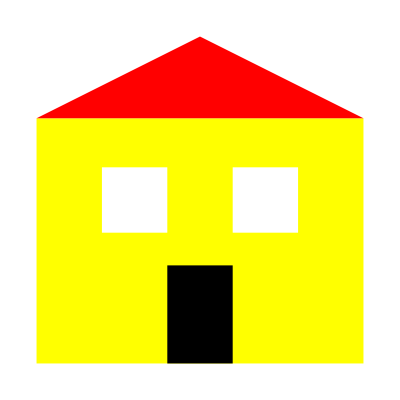

```mathematica
hisica={{Yellow,Rectangle[{0,0},{1,0.75}]},
{Black, Rectangle[{0.4,0},{0.6,0.3}]},
{White, Rectangle[{0.2,0.4},{0.4,0.6}]},
{White, Rectangle[{0.6,0.4},{0.8,0.6}]},
{Red, Polygon[{{0,0.75},{0.5,1},{1,0.75}}]}
};
Graphics[hisica]
```

```mathematica
Graphics[f[hisica]]
```

-Graphics-

```mathematica
Manipulate[Graphics[Nest[f,hisica,n],Axes->True],{n,0,6,1}]
```